```mathematica
data=Import["/Users/shreyadas/Desktop/cleaned_layoffs_data.csv"]
Length[data]
```

1176

Bar Chart for Distribution of Companies by Industry:

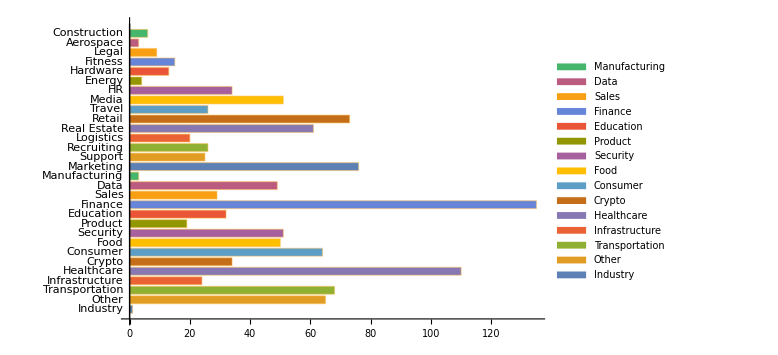

```mathematica
industryCounts=Counts[data[[All,3]]];
colors=ColorData[97,"ColorList"];
BarChart[industryCounts,ChartLegends->Automatic,ChartStyle->colors,BarOrigin->Left,ChartLabels->Placed[Automatic,Before],ImageSize->Large]
```

Visualization for Laid_Off_Count vs. Year:

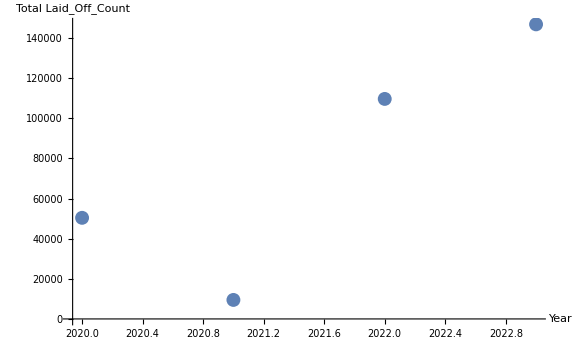

```mathematica
ListPlot[Tooltip[{#[[1,7]],Total[#[[All,6]]]},#[[1,7]]]&/@SortBy[GatherBy[data,Last],First],PlotStyle->AbsolutePointSize[10],AxesLabel->{"Year","Total Laid_Off_Count"},ImageSize->Large]
```

GeographicMap for Company Locations:

```mathematica
cities=data[All,{Entity["City",#2],#6}&];

GeoListPlot[cities,GeoLabels->(Tooltip[#2,#3]&),PlotMarkers->Style["*",30],ImageSize->Large]
```

GeoListPlot[$Failed[All,{Entity[City,#2],#6}&],GeoLabels→(#2&),PlotMarkers→*,ImageSize→Large]

GeoListPlot::ngeoents: $Failed[All,{Entity[City,#2],#6}&] is not a list or nested list of geographical entities

GeoListPlot[$Failed[All,{Entity[City,#2],#6}&],GeoLabels→(#2&),PlotMarkers→ψ,ImageSize→Large]

```mathematica
GeoGraphics[{GeoMarker[#1,"Scale"->#2/1000]&@@@Transpose[{layoffs[["City"]],layoffs[["Laid_Off_Count"]]}]},GeoRange->Entity["Country","UnitedStates"],GeoRangePadding->Full,ImageSize->Large]
```

Part::pspec1: Part specification City is not applicable.

Part::pspec1: Part specification Laid_Off_Count is not applicable.

GeoMarker::invpts: layoffs is not a valid GeoMarker coordinates specification.

-Graphics-